```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WLEDUI.xlsx"]
```

```mathematica
data1={{10.,2.99},{11.,3.01},{12.,3.03},{12.9,3.05},{14.5,3.08},{16.,3.1},{17.5,3.12},{19.,3.14},{20.9,3.16},{22.9,3.18},{25.,3.21},{27.,3.24},{29.,3.26},{31.,3.28},{33.,3.3},{34.,3.32},{35.,3.33},{37.,3.35},{39.,3.38},{40.,3.39}};
Import["C:\\Users\\Juntao Yu\\Desktop\\LED\\WLEDIL.xlsx"]
```

```mathematica
data2={{10.,2.417},{11.,2.586},{12.,2.783},{12.9,2.974},{14.5,3.215},{16.,3.473},{17.5,3.685},{19.,3.927},{20.9,4.202},{22.9,4.444},{25.,4.729},{27.,4.957},{29.,5.164},{31.,5.371},{33.,5.55},{34.,5.633},{35.,5.704},{37.,5.9},{39.,6.136},{40.,6.339}};
```

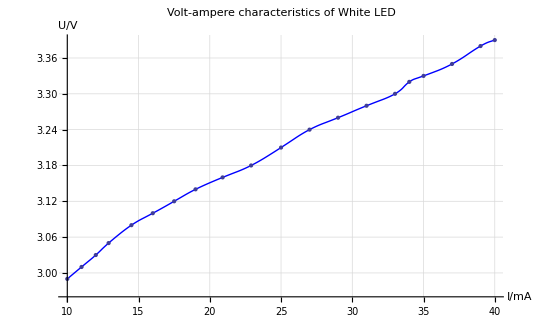

```mathematica
Show[gra1=ListLinePlot[data1,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"I/mA","U/V"},PlotLabel->"Volt-ampere characteristics of White LED",GridLines->Automatic],ListPlot[data1]]
```

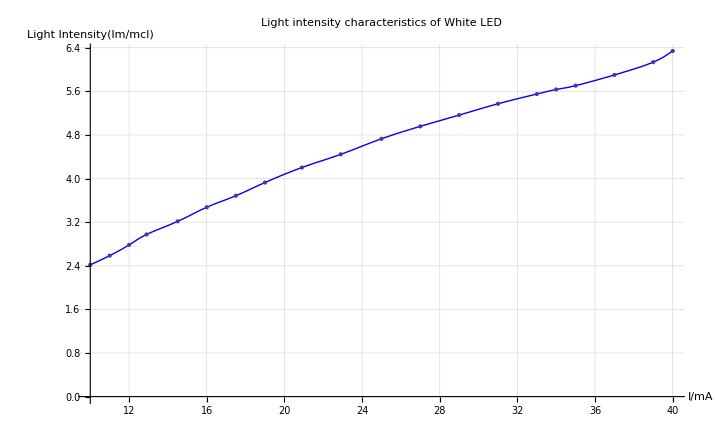

```mathematica
Show[gra2=ListLinePlot[data2,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"I/mA","Light Intensity(lm/mcl)"},PlotLabel->"Light intensity characteristics of White LED",GridLines->Automatic],ListPlot[data2]]
```